```mathematica
InitialAngle=45Degree
```

45 °

```mathematica
InitialSpeed=100.0
```

100.

```mathematica
Gravity=-9.81
```

-9.81

```mathematica
InitialVelocityX=InitialSpeed*Cos[InitialAngle]
```

70.7107

```mathematica
InitialVelocityY=InitialSpeed*Sin[InitialAngle]
```

70.7107

```mathematica
ProjectileX[t_]:=InitialVelocityX*t
```

```mathematica
ProjectileY[t_]:=InitialVelocityY*t+(0.5)*Gravity*t^2
```

```mathematica
MaxTime=15
```

15

Below is a graph of the true path of the projectile.

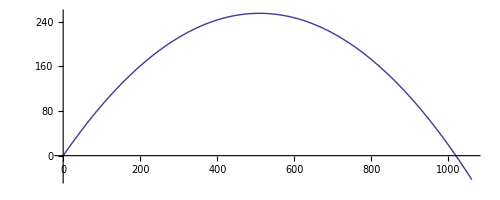

```mathematica
ParametricPlot[{ProjectileX[t], ProjectileY[t]},{t,0,MaxTime}]
```

```mathematica
NoiseLevel=10.0
```

10.

```mathematica
NoisyProjectileX[t_]:=RandomVariate[NormalDistribution[ProjectileX[t],NoiseLevel]]
```

```mathematica
NoisyProjectileY[t_]:=RandomVariate[NormalDistribution[ProjectileY[t],NoiseLevel]]
```

Assuming no friction, etc., Newton’s laws of motion state that the X-velocity will be constant, while the Y-velocity will be affected by gravity. These will become the “control updates” input into the Kalman filter.

```mathematica
VelocityX[t_]:=ProjectileX'[t]
```

```mathematica
VelocityY[t_]:=ProjectileY'[t]
```

```mathematica
InitalVelocity={InitialVelocityX,InitialVelocityY}
```

{70.7107,70.7107}

```mathematica
InitialAcceleration={0,0}
```

{0,0}

Δt represents our timestep.

```mathematica
Δt=0.1
```

0.1

A is the state transition matrix. Multiply the previous state by A to obtain the new state. (Note: ExampleA is displayed in “hold” form to preserve variables; the value A is actually evaluated.)

```mathematica
ExampleA={{1, HoldForm[Δt], 0, 0}, {0, 1, 0, 0}, {0, 0, 1, HoldForm[Δt]}, {0, 0, 0, 1}}
```

{{1,Δt,0,0},{0,1,0,0},{0,0,1,Δt},{0,0,0,1}}

```mathematica
A=ReleaseHold[ExampleA]
```

{{1,0.1,0,0},{0,1,0,0},{0,0,1,0.1},{0,0,0,1}}

B is the control matrix. Multiply any control factors by B. Note that only the third (y-position) and fourth rows (y-velocity) will have control values.

```mathematica
B={{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}
```

{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}}

Note that multiplying A by the state vector and adding B multiplied by the control vector gives us the kinematic equations:

```mathematica
ExampleState=Transpose[{{X_,VelocityX_,Y_,VelocityY_}}]
```

{{X_},{VelocityX_},{Y_},{VelocityY_}}

```mathematica
ExampleControl=Transpose[{{0, 0, HoldForm[(0.5)*Gravity*Δt^2],HoldForm[Gravity*Δt]}}]
```

{{0},{0},{0.5 Gravity Δt^2},{Gravity Δt}}

(Note: ExampleControl is displayed in “hold” form whereas ControlVector is evaluated because it needs to be used later on.)

```mathematica
ControlVector=ReleaseHold[ExampleControl]
```

{{0},{0},{-0.04905},{-0.981}}

```mathematica
AExample.ExampleState+B.ExampleControl//MatrixForm
```

(Δt VelocityX_+X_
VelocityX_
0.5 Gravity Δt^2+Δt VelocityY_+Y_
Gravity Δt+VelocityY_)

H is the observation matrix. Multiply an incoming observation by H to obtain a state. In this case, we don’t modify the observations beforehand.

```mathematica
H=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

Q is the process covariance; assume no process error.

```mathematica
Q=ConstantArray[0, {4,4}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

R is the measurement covariance; also very small.

```mathematica
R=IdentityMatrix[4]*0.2
```

{{0.2,0.,0.,0.},{0.,0.2,0.,0.},{0.,0.,0.2,0.},{0.,0.,0.,0.2}}

X0 is the initial prediction for the state; we will set it to a vastly incorrect value (initially at (0, 500) and wrong speed).

```mathematica
Wrongness=2.0
```

2.

```mathematica
X0=Transpose[{{0, Wrongness*InitialVelocityX,500,Wrongness*InitialVelocityY}}]
```

{{0},{141.421},{500},{141.421}}

P0 is the initial prediction for the covariance.

```mathematica
P0=IdentityMatrix[4]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
KalmanStep[A_,B_,H_,Q_,R_,{X_,P_},NewMeasurement_,NewControl_]:=(
(* Prediction step. *)
predictedStateEstimate=A.X + B.NewControl;
predictedProbEstimate = (A.P).Transpose[A]+Q;
(* Observation step. *)
innovation = NewMeasurement-H.predictedStateEstimate;
innovationCovariance = (H.predictedProbEstimate).Transpose[H]+R;
(* Update step. *)
kalmanGain = (predictedProbEstimate.Transpose[H]).Inverse[innovationCovariance];
newStateEstimate=predictedStateEstimate+kalmanGain.innovation;
size=First[Dimensions[P]];
newProbEstimate=(IdentityMatrix[size]-kalmanGain.H).predictedProbEstimate;
{newStateEstimate,newProbEstimate}
)
```

```mathematica
KalmanProjectileMapping[OldStateProb_,NewMeasurement_]:=KalmanStep[A,B,H,Q,R,OldStateProb,NewMeasurement,ControlVector]
```

The input to the Kalman filter consists of the X-pos, X-vel, Y-pos, and Y-vel. We simulate that X- and Y-positions are measured with noise, whereas the X- and Y-velocities are measured relatively accurately.

```mathematica
NoisySamples=Map[(Transpose[{{NoisyProjectileX[#],VelocityX[#],NoisyProjectileY[#],VelocityY[#]}}])&,Range[0,MaxTime,Δt]]
```

{{{5.0071},{70.7107},{-2.30151},{70.7107}},{{9.26859},{70.7107},{24.8432},{69.7297}},{{7.37036},{70.7107},{12.2247},{68.7487}},{{18.2149},{70.7107},{27.0576},{67.7677}},{{25.5674},{70.7107},{39.6398},{66.7867}},{{39.727},{70.7107},{39.8896},{65.8057}},{{41.8645},{70.7107},{28.6217},{64.8247}},{{55.7899},{70.7107},{44.918},{63.8437}},{{63.396},{70.7107},{54.0227},{62.8627}},{{79.112},{70.7107},{49.6052},{61.8817}},{{70.6185},{70.7107},{50.861},{60.9007}},{{77.7615},{70.7107},{60.7506},{59.9197}},{{99.8718},{70.7107},{70.3497},{58.9387}},{{90.3936},{70.7107},{78.3271},{57.9577}},{{102.127},{70.7107},{70.4562},{56.9767}},{{99.2159},{70.7107},{82.8075},{55.9957}},{{122.274},{70.7107},{111.192},{55.0147}},{{118.683},{70.7107},{99.3464},{54.0337}},{{105.936},{70.7107},{94.1414},{53.0527}},{{133.036},{70.7107},{107.912},{52.0717}},{{153.699},{70.7107},{115.532},{51.0907}},{{147.363},{70.7107},{117.125},{50.1097}},{{162.968},{70.7107},{127.154},{49.1287}},{{177.768},{70.7107},{143.425},{48.1477}},{{169.225},{70.7107},{151.511},{47.1667}},{{176.042},{70.7107},{165.446},{46.1857}},{{178.333},{70.7107},{156.578},{45.2047}},{{184.584},{70.7107},{148.029},{44.2237}},{{200.942},{70.7107},{161.376},{43.2427}},{{202.971},{70.7107},{165.568},{42.2617}},{{211.191},{70.7107},{147.838},{41.2807}},{{220.74},{70.7107},{187.62},{40.2997}},{{227.417},{70.7107},{186.642},{39.3187}},{{244.511},{70.7107},{173.195},{38.3377}},{{256.09},{70.7107},{179.324},{37.3567}},{{240.59},{70.7107},{190.611},{36.3757}},{{241.669},{70.7107},{175.61},{35.3947}},{{269.714},{70.7107},{208.453},{34.4137}},{{266.486},{70.7107},{215.957},{33.4327}},{{276.363},{70.7107},{204.079},{32.4517}},{{277.759},{70.7107},{214.893},{31.4707}},{{280.702},{70.7107},{207.779},{30.4897}},{{298.312},{70.7107},{199.885},{29.5087}},{{322.107},{70.7107},{224.211},{28.5277}},{{309.992},{70.7107},{215.545},{27.5467}},{{316.873},{70.7107},{222.192},{26.5657}},{{332.829},{70.7107},{219.257},{25.5847}},{{329.133},{70.7107},{231.384},{24.6037}},{{334.224},{70.7107},{227.481},{23.6227}},{{343.721},{70.7107},{217.355},{22.6417}},{{353.327},{70.7107},{226.258},{21.6607}},{{361.258},{70.7107},{226.046},{20.6797}},{{386.957},{70.7107},{238.176},{19.6987}},{{387.319},{70.7107},{229.532},{18.7177}},{{378.921},{70.7107},{269.333},{17.7367}},{{379.114},{70.7107},{236.732},{16.7557}},{{395.501},{70.7107},{240.599},{15.7747}},{{399.593},{70.7107},{246.176},{14.7937}},{{411.851},{70.7107},{248.841},{13.8127}},{{413.872},{70.7107},{255.1},{12.8317}},{{438.579},{70.7107},{259.205},{11.8507}},{{426.855},{70.7107},{253.995},{10.8697}},{{436.588},{70.7107},{250.608},{9.88868}},{{439.758},{70.7107},{262.08},{8.90768}},{{462.782},{70.7107},{259.614},{7.92668}},{{472.304},{70.7107},{242.756},{6.94568}},{{458.142},{70.7107},{261.912},{5.96468}},{{460.776},{70.7107},{244.419},{4.98368}},{{476.045},{70.7107},{249.74},{4.00268}},{{487.411},{70.7107},{260.076},{3.02168}},{{506.692},{70.7107},{241.923},{2.04068}},{{492.425},{70.7107},{258.597},{1.05968}},{{516.226},{70.7107},{265.838},{0.0786781}},{{492.851},{70.7107},{249.675},{-0.902322}},{{525.527},{70.7107},{249.861},{-1.88332}},{{536.015},{70.7107},{267.672},{-2.86432}},{{550.571},{70.7107},{262.421},{-3.84532}},{{555.974},{70.7107},{243.174},{-4.82632}},{{555.414},{70.7107},{248.979},{-5.80732}},{{556.905},{70.7107},{261.741},{-6.78832}},{{566.777},{70.7107},{258.511},{-7.76932}},{{602.691},{70.7107},{251.622},{-8.75032}},{{577.658},{70.7107},{243.631},{-9.73132}},{{580.908},{70.7107},{257.158},{-10.7123}},{{598.105},{70.7107},{240.323},{-11.6933}},{{595.954},{70.7107},{234.106},{-12.6743}},{{605.971},{70.7107},{243.199},{-13.6553}},{{600.859},{70.7107},{262.276},{-14.6363}},{{610.708},{70.7107},{246.004},{-15.6173}},{{629.356},{70.7107},{244.746},{-16.5983}},{{645.212},{70.7107},{243.521},{-17.5793}},{{669.342},{70.7107},{242.472},{-18.5603}},{{650.844},{70.7107},{232.031},{-19.5413}},{{663.433},{70.7107},{245.746},{-20.5223}},{{662.42},{70.7107},{228.571},{-21.5033}},{{663.077},{70.7107},{232.889},{-22.4843}},{{685.881},{70.7107},{243.912},{-23.4653}},{{692.822},{70.7107},{216.373},{-24.4463}},{{685.59},{70.7107},{216.218},{-25.4273}},{{691.681},{70.7107},{213.031},{-26.4083}},{{707.372},{70.7107},{223.076},{-27.3893}},{{716.362},{70.7107},{199.644},{-28.3703}},{{742.841},{70.7107},{210.089},{-29.3513}},{{723.239},{70.7107},{196.769},{-30.3323}},{{742.798},{70.7107},{200.146},{-31.3133}},{{744.006},{70.7107},{186.179},{-32.2943}},{{738.435},{70.7107},{179.561},{-33.2753}},{{756.038},{70.7107},{189.883},{-34.2563}},{{748.088},{70.7107},{187.793},{-35.2373}},{{781.801},{70.7107},{195.761},{-36.2183}},{{778.747},{70.7107},{189.241},{-37.1993}},{{784.957},{70.7107},{179.374},{-38.1803}},{{793.65},{70.7107},{191.568},{-39.1613}},{{800.012},{70.7107},{176.31},{-40.1423}},{{822.041},{70.7107},{145.562},{-41.1233}},{{794.873},{70.7107},{155.76},{-42.1043}},{{816.638},{70.7107},{174.131},{-43.0853}},{{827.118},{70.7107},{151.089},{-44.0663}},{{817.519},{70.7107},{153.424},{-45.0473}},{{848.377},{70.7107},{160.257},{-46.0283}},{{838.836},{70.7107},{143.399},{-47.0093}},{{855.066},{70.7107},{131.633},{-47.9903}},{{882.117},{70.7107},{117.02},{-48.9713}},{{879.116},{70.7107},{128.8},{-49.9523}},{{897.335},{70.7107},{131.468},{-50.9333}},{{875.591},{70.7107},{133.236},{-51.9143}},{{887.55},{70.7107},{119.544},{-52.8953}},{{909.554},{70.7107},{112.391},{-53.8763}},{{903.569},{70.7107},{102.59},{-54.8573}},{{897.184},{70.7107},{89.5124},{-55.8383}},{{906.746},{70.7107},{93.1429},{-56.8193}},{{917.064},{70.7107},{105.977},{-57.8003}},{{927.507},{70.7107},{76.8581},{-58.7813}},{{942.298},{70.7107},{80.163},{-59.7623}},{{960.374},{70.7107},{66.8921},{-60.7433}},{{949.049},{70.7107},{49.744},{-61.7243}},{{954.546},{70.7107},{39.7447},{-62.7053}},{{964.363},{70.7107},{57.0236},{-63.6863}},{{967.886},{70.7107},{31.9423},{-64.6673}},{{995.795},{70.7107},{39.4798},{-65.6483}},{{987.296},{70.7107},{39.6983},{-66.6293}},{{989.381},{70.7107},{13.0647},{-67.6103}},{{991.408},{70.7107},{15.0758},{-68.5913}},{{1017.24},{70.7107},{2.28116},{-69.5723}},{{1034.19},{70.7107},{7.74961},{-70.5533}},{{1014.65},{70.7107},{-3.53536},{-71.5343}},{{1033.43},{70.7107},{-15.7934},{-72.5153}},{{1024.62},{70.7107},{-25.5107},{-73.4963}},{{1051.91},{70.7107},{-29.3744},{-74.4773}},{{1033.68},{70.7107},{-32.9955},{-75.4583}},{{1059.51},{70.7107},{-38.6286},{-76.4393}}}

```mathematica
KalmanData=FoldList[KalmanProjectileMapping,{X0,P0},NoisySamples]
```

{{{{0},{141.421},{500},{141.421}},{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}},{{{5.54676},{82.4508},{82.6778},{75.2507}},{{0.166713,0.00277393,0.,0.},{0.00277393,0.166436,0.,0.},{0.,0.,0.166713,0.00277393},{0.,0.,0.00277393,0.166436}}},{{{11.3893},{77.0061},{60.2167},{70.3332}},{{0.0912757,0.00576132,0.,0.},{0.00576132,0.090535,0.,0.},{0.,0.,0.0912757,0.00576132},{0.,0.,0.00576132,0.090535}}},{{{15.1622},{74.647},{49.7842},{67.2489}},{{0.0632843,0.00697134,0.,0.},{0.00697134,0.0619675,0.,0.},{0.,0.,0.0632843,0.00697134},{0.,0.,0.00697134,0.0619675}}},{{{21.3997},{73.5558},{49.3356},{65.5028}},{{0.0488492,0.00759777,0.,0.},{0.00759777,0.0469274,0.,0.},{0.,0.,0.0488492,0.00759777},{0.,0.,0.00759777,0.0469274}}},{{{28.0022},{72.8939},{52.6758},{64.3034}},{{0.0401447,0.0079566,0.,0.},{0.0079566,0.037613,0.,0.},{0.,0.,0.0401447,0.0079566},{0.,0.,0.0079566,0.037613}}},{{{35.9652},{72.7338},{55.8625},{62.9278}},{{0.034392,0.00816697,0.,0.},{0.00816697,0.0312563,0.,0.},{0.,0.,0.034392,0.00816697},{0.,0.,0.00816697,0.0312563}}},{{{42.9462},{72.4076},{57.1433},{60.943}},{{0.030355,0.00828402,0.,0.},{0.00828402,0.0266272,0.,0.},{0.,0.,0.030355,0.00828402},{0.,0.,0.00828402,0.0266272}}},{{{50.8838},{72.4452},{60.8473},{59.6487}},{{0.0273997,0.00833709,0.,0.},{0.00833709,0.023096,0.,0.},{0.,0.,0.0273997,0.00833709},{0.,0.,0.00833709,0.023096}}},{{{58.7189},{72.4888},{65.3349},{58.5621}},{{0.0251672,0.00834345,0.,0.},{0.00834345,0.0203068,0.,0.},{0.,0.,0.0251672,0.00834345},{0.,0.,0.00834345,0.0203068}}},{{{67.4343},{72.8748},{68.7969},{57.0738}},{{0.0234389,0.00831417,0.,0.},{0.00831417,0.0180435,0.,0.},{0.,0.,0.0234389,0.00831417},{0.,0.,0.00831417,0.0180435}}},{{{74.1795},{72.5305},{72.0496},{55.5074}},{{0.022074,0.00825683,0.,0.},{0.00825683,0.0161672,0.,0.},{0.,0.,0.022074,0.00825683},{0.,0.,0.00825683,0.0161672}}},{{{80.9731},{72.2477},{76.0096},{54.2328}},{{0.0209779,0.00817693,0.,0.},{0.00817693,0.0145846,0.,0.},{0.,0.,0.0209779,0.00817693},{0.,0.,0.00817693,0.0145846}}},{{{89.3081},{72.6175},{80.5054},{53.1823}},{{0.0200844,0.00807866,0.,0.},{0.00807866,0.0132306,0.,0.},{0.,0.,0.0200844,0.00807866},{0.,0.,0.00807866,0.0132306}}},{{{95.8965},{72.2566},{85.2835},{52.2517}},{{0.0193461,0.00796535,0.,0.},{0.00796535,0.0120584,0.,0.},{0.,0.,0.0193461,0.00796535},{0.,0.,0.00796535,0.0120584}}},{{{102.968},{72.1323},{88.8101},{50.8014}},{{0.0187282,0.00783972,0.,0.},{0.00783972,0.0110337,0.,0.},{0.,0.,0.0187282,0.00783972},{0.,0.,0.00783972,0.0110337}}},{{{109.129},{71.6379},{93.0748},{49.7082}},{{0.0182046,0.00770404,0.,0.},{0.00770404,0.0101303,0.,0.},{0.,0.,0.0182046,0.00770404},{0.,0.,0.00770404,0.0101303}}},{{{116.788},{71.8208},{99.4057},{49.5192}},{{0.0177552,0.00756027,0.,0.},{0.00756027,0.00932831,0.,0.},{0.,0.,0.0177552,0.00756027},{0.,0.,0.00756027,0.00932831}}},{{{123.47},{71.5771},{104.081},{48.591}},{{0.0173649,0.00741007,0.,0.},{0.00741007,0.00861196,0.,0.},{0.,0.,0.0173649,0.00741007},{0.,0.,0.00741007,0.00861196}}},{{{128.495},{70.6469},{107.833},{47.2918}},{{0.0170217,0.00725492,0.,0.},{0.00725492,0.00796879,0.,0.},{0.,0.,0.0170217,0.00725492},{0.,0.,0.00725492,0.00796879}}},{{{135.351},{70.5597},{112.333},{46.3604}},{{0.016716,0.00709609,0.,0.},{0.00709609,0.00738871,0.,0.},{0.,0.,0.016716,0.00709609},{0.,0.,0.00709609,0.00738871}}},{{{143.341},{70.9564},{117.004},{45.5272}},{{0.0164406,0.00693471,0.,0.},{0.00693471,0.00686348,0.,0.},{0.,0.,0.0164406,0.00693471},{0.,0.,0.00693471,0.00686348}}},{{{150.179},{70.8445},{121.341},{44.5755}},{{0.0161895,0.00677176,0.,0.},{0.00677176,0.00638628,0.,0.},{0.,0.,0.0161895,0.00677176},{0.,0.,0.00677176,0.00638628}}},{{{157.714},{71.029},{126.045},{43.8056}},{{0.015958,0.00660811,0.,0.},{0.00660811,0.0059514,0.,0.},{0.,0.,0.015958,0.00660811},{0.,0.,0.00660811,0.0059514}}},{{{165.826},{71.4374},{131.575},{43.3928}},{{0.0157422,0.00644451,0.,0.},{0.00644451,0.00555403,0.,0.},{0.,0.,0.0157422,0.00644451},{0.,0.,0.00644451,0.00555403}}},{{{172.656},{71.301},{137.23},{43.0266}},{{0.0155392,0.0062816,0.,0.},{0.0062816,0.00519004,0.,0.},{0.,0.,0.0155392,0.0062816},{0.,0.,0.0062816,0.00519004}}},{{{179.481},{71.172},{143.449},{42.8794}},{{0.0153466,0.00611996,0.,0.},{0.00611996,0.00485593,0.,0.},{0.,0.,0.0153466,0.00611996},{0.,0.,0.00611996,0.00485593}}},{{{185.958},{70.9153},{148.46},{42.2385}},{{0.0151624,0.00596007,0.,0.},{0.00596007,0.00454865,0.,0.},{0.,0.,0.0151624,0.00596007},{0.,0.,0.00596007,0.00454865}}},{{{192.409},{70.6653},{152.376},{41.1871}},{{0.014985,0.00580233,0.,0.},{0.00580233,0.00426553,0.,0.},{0.,0.,0.014985,0.00580233},{0.,0.,0.00580233,0.00426553}}},{{{199.586},{70.7076},{156.897},{40.4061}},{{0.0148133,0.00564709,0.,0.},{0.00564709,0.00400425,0.,0.},{0.,0.,0.0148133,0.00564709},{0.,0.,0.00564709,0.00400425}}},{{{206.387},{70.6064},{161.309},{39.607}},{{0.0146462,0.00549464,0.,0.},{0.00549464,0.00376277,0.,0.},{0.,0.,0.0146462,0.00549464},{0.,0.,0.00549464,0.00376277}}},{{{213.287},{70.548},{164.033},{38.2085}},{{0.0144829,0.00534522,0.,0.},{0.00534522,0.00353928,0.,0.},{0.,0.,0.0144829,0.00534522},{0.,0.,0.00534522,0.00353928}}},{{{220.374},{70.561},{169.304},{37.7937}},{{0.0143229,0.005199,0.,0.},{0.005199,0.00333216,0.,0.},{0.,0.,0.0143229,0.005199},{0.,0.,0.005199,0.00333216}}},{{{227.433},{70.5631},{174.061},{37.1961}},{{0.0141657,0.00505614,0.,0.},{0.00505614,0.00313999,0.,0.},{0.,0.,0.0141657,0.00505614},{0.,0.,0.00505614,0.00313999}}},{{{235.195},{70.8116},{177.466},{36.135}},{{0.0140109,0.00491674,0.,0.},{0.00491674,0.00296147,0.,0.},{0.,0.,0.0140109,0.00491674},{0.,0.,0.00491674,0.00296147}}},{{{243.231},{71.1404},{180.965},{35.144}},{{0.0138582,0.00478089,0.,0.},{0.00478089,0.00279547,0.,0.},{0.,0.,0.0138582,0.00478089},{0.,0.,0.00478089,0.00279547}}},{{{249.666},{70.908},{184.905},{34.3359}},{{0.0137075,0.00464863,0.,0.},{0.00464863,0.00264094,0.,0.},{0.,0.,0.0137075,0.00464863},{0.,0.,0.00464863,0.00264094}}},{{{255.73},{70.5645},{187.476},{33.0938}},{{0.0135585,0.00451999,0.,0.},{0.00451999,0.00249694,0.,0.},{0.,0.,0.0135585,0.00451999},{0.,0.,0.00451999,0.00249694}}},{{{263.254},{70.7185},{191.975},{32.5293}},{{0.0134112,0.00439498,0.,0.},{0.00439498,0.00236263,0.,0.},{0.,0.,0.0134112,0.00439498},{0.,0.,0.00439498,0.00236263}}},{{{270.071},{70.6363},{196.597},{32.0133}},{{0.0132655,0.00427358,0.,0.},{0.00427358,0.00223724,0.,0.},{0.,0.,0.0132655,0.00427358},{0.,0.,0.00427358,0.00223724}}},{{{277.086},{70.6211},{200.063},{31.1373}},{{0.0131213,0.00415577,0.,0.},{0.00415577,0.00212007,0.,0.},{0.,0.,0.0131213,0.00415577},{0.,0.,0.00415577,0.00212007}}},{{{283.735},{70.4929},{203.918},{30.4073}},{{0.0129786,0.0040415,0.,0.},{0.0040415,0.0020105,0.,0.},{0.,0.,0.0129786,0.0040415},{0.,0.,0.0040415,0.0020105}}},{{{290.141},{70.2968},{206.986},{29.4535}},{{0.0128374,0.00393072,0.,0.},{0.00393072,0.00190794,0.,0.},{0.,0.,0.0128374,0.00393072},{0.,0.,0.00393072,0.00190794}}},{{{297.251},{70.3224},{209.268},{28.2908}},{{0.0126976,0.00382337,0.,0.},{0.00382337,0.00181186,0.,0.},{0.,0.,0.0126976,0.00382337},{0.,0.,0.00382337,0.00181186}}},{{{305.41},{70.6572},{212.834},{27.5465}},{{0.0125594,0.00371939,0.,0.},{0.00371939,0.00172179,0.,0.},{0.,0.,0.0125594,0.00371939},{0.,0.,0.00371939,0.00172179}}},{{{312.323},{70.6127},{215.558},{26.5736}},{{0.0124227,0.00361869,0.,0.},{0.00361869,0.00163729,0.,0.},{0.,0.,0.0124227,0.00361869},{0.,0.,0.00361869,0.00163729}}},{{{319.231},{70.5692},{218.431},{25.6711}},{{0.0122876,0.00352121,0.,0.},{0.00352121,0.00155794,0.,0.},{0.,0.,0.0122876,0.00352121},{0.,0.,0.00352121,0.00155794}}},{{{326.688},{70.6824},{220.861},{24.6677}},{{0.0121539,0.00342686,0.,0.},{0.00342686,0.00148338,0.,0.},{0.,0.,0.0121539,0.00342686},{0.,0.,0.00342686,0.00148338}}},{{{333.479},{70.6054},{223.781},{23.8284}},{{0.0120218,0.00333556,0.,0.},{0.00333556,0.00141327,0.,0.},{0.,0.,0.0120218,0.00333556},{0.,0.,0.00333556,0.00141327}}},{{{340.166},{70.5036},{226.209},{22.8748}},{{0.0118914,0.00324721,0.,0.},{0.00324721,0.0013473,0.,0.},{0.,0.,0.0118914,0.00324721},{0.,0.,0.00324721,0.0013473}}},{{{347.014},{70.4497},{227.807},{21.7232}},{{0.0117625,0.00316175,0.,0.},{0.00316175,0.00128518,0.,0.},{0.,0.,0.0117625,0.00316175},{0.,0.,0.00316175,0.00128518}}},{{{354.02},{70.44},{229.731},{20.6913}},{{0.0116352,0.00307906,0.,0.},{0.00307906,0.00122664,0.,0.},{0.,0.,0.0116352,0.00307906},{0.,0.,0.00307906,0.00122664}}},{{{361.079},{70.4445},{231.437},{19.6304}},{{0.0115095,0.00299908,0.,0.},{0.00299908,0.00117145,0.,0.},{0.,0.,0.0115095,0.00299908},{0.,0.,0.00299908,0.00117145}}},{{{369.2},{70.7211},{233.641},{18.7258}},{{0.0113855,0.00292171,0.,0.},{0.00292171,0.00111937,0.,0.},{0.,0.,0.0113855,0.00292171},{0.,0.,0.00292171,0.00111937}}},{{{376.894},{70.8783},{235.144},{17.6656}},{{0.0112631,0.00284688,0.,0.},{0.00284688,0.00107019,0.,0.},{0.,0.,0.0112631,0.00284688},{0.,0.,0.00284688,0.00107019}}},{{{383.698},{70.8073},{238.685},{17.1404}},{{0.0111424,0.00277448,0.,0.},{0.00277448,0.00102374,0.,0.},{0.,0.,0.0111424,0.00277448},{0.,0.,0.00277448,0.00102374}}},{{{390.134},{70.6491},{240.159},{16.1134}},{{0.0110234,0.00270445,0.,0.},{0.00270445,0.000979822,0.,0.},{0.,0.,0.0110234,0.00270445},{0.,0.,0.00270445,0.000979822}}},{{{397.107},{70.627},{241.669},{15.1206}},{{0.010906,0.0026367,0.,0.},{0.0026367,0.000938279,0.,0.},{0.,0.,0.010906,0.0026367},{0.,0.,0.0026367,0.000938279}}},{{{403.924},{70.5685},{243.304},{14.1817}},{{0.0107903,0.00257115,0.,0.},{0.00257115,0.000898959,0.,0.},{0.,0.,0.0107903,0.00257115},{0.,0.,0.00257115,0.000898959}}},{{{411.029},{70.58},{244.904},{13.2556}},{{0.0106762,0.00250772,0.,0.},{0.00250772,0.00086172,0.,0.},{0.,0.,0.0106762,0.00250772},{0.,0.,0.00250772,0.00086172}}},{{{417.866},{70.529},{246.658},{12.386}},{{0.0105638,0.00244635,0.,0.},{0.00244635,0.000826432,0.,0.},{0.,0.,0.0105638,0.00244635},{0.,0.,0.00244635,0.000826432}}},{{{425.635},{70.6928},{248.446},{11.5423}},{{0.010453,0.00238695,0.,0.},{0.00238695,0.000792972,0.,0.},{0.,0.,0.010453,0.00238695},{0.,0.,0.00238695,0.000792972}}},{{{432.402},{70.6247},{249.785},{10.6142}},{{0.0103439,0.00232946,0.,0.},{0.00232946,0.000761229,0.,0.},{0.,0.,0.0103439,0.00232946},{0.,0.,0.00232946,0.000761229}}},{{{439.318},{70.5923},{250.791},{9.63201}},{{0.0102364,0.0022738,0.,0.},{0.0022738,0.000731097,0.,0.},{0.,0.,0.0102364,0.0022738},{0.,0.,0.0022738,0.000731097}}},{{{446.044},{70.5193},{252.233},{8.76706}},{{0.0101305,0.00221992,0.,0.},{0.00221992,0.000702479,0.,0.},{0.,0.,0.0101305,0.00221992},{0.,0.,0.00221992,0.000702479}}},{{{453.583},{70.6249},{253.391},{7.85756}},{{0.0100262,0.00216775,0.,0.},{0.00216775,0.000675285,0.,0.},{0.,0.,0.0100262,0.00216775},{0.,0.,0.00216775,0.000675285}}},{{{461.225},{70.7486},{253.564},{6.75641}},{{0.00992353,0.00211722,0.,0.},{0.00211722,0.000649429,0.,0.},{0.,0.,0.00992353,0.00211722},{0.,0.,0.00211722,0.000649429}}},{{{467.801},{70.6434},{254.572},{5.85585}},{{0.00982242,0.00206827,0.,0.},{0.00206827,0.000624834,0.,0.},{0.,0.,0.00982242,0.00206827},{0.,0.,0.00206827,0.000624834}}},{{{474.181},{70.5013},{254.59},{4.76717}},{{0.00972287,0.00202086,0.,0.},{0.00202086,0.000601425,0.,0.},{0.,0.,0.00972287,0.00202086},{0.,0.,0.00202086,0.000601425}}},{{{480.983},{70.4507},{254.766},{3.73469}},{{0.00962486,0.00197492,0.,0.},{0.00197492,0.000579135,0.,0.},{0.,0.,0.00962486,0.00197492},{0.,0.,0.00197492,0.000579135}}},{{{488.001},{70.4454},{255.33},{2.80256}},{{0.00952838,0.00193039,0.,0.},{0.00193039,0.000557898,0.,0.},{0.,0.,0.00952838,0.00193039},{0.,0.,0.00193039,0.000557898}}},{{{495.598},{70.556},{254.92},{1.69345}},{{0.00943339,0.00188723,0.,0.},{0.00188723,0.000537656,0.,0.},{0.,0.,0.00943339,0.00188723},{0.,0.,0.00188723,0.000537656}}},{{{502.177},{70.4621},{255.21},{0.746167}},{{0.0093399,0.0018454,0.,0.},{0.0018454,0.000518353,0.,0.},{0.,0.,0.0093399,0.0018454},{0.,0.,0.0018454,0.000518353}}},{{{509.549},{70.5259},{255.728},{-0.138372}},{{0.00924786,0.00180483,0.,0.},{0.00180483,0.000499937,0.,0.},{0.,0.,0.00924786,0.00180483},{0.,0.,0.00180483,0.000499937}}},{{{515.516},{70.3167},{255.393},{-1.17173}},{{0.00915727,0.00176548,0.,0.},{0.00176548,0.000482358,0.,0.},{0.,0.,0.00915727,0.00176548},{0.,0.,0.00176548,0.000482358}}},{{{522.686},{70.3433},{254.986},{-2.19844}},{{0.0090681,0.00172732,0.,0.},{0.00172732,0.000465571,0.,0.},{0.,0.,0.0090681,0.00172732},{0.,0.,0.00172732,0.000465571}}},{{{530.006},{70.3973},{255.301},{-3.06924}},{{0.00898034,0.00169029,0.,0.},{0.00169029,0.000449532,0.,0.},{0.,0.,0.00898034,0.00169029},{0.,0.,0.00169029,0.000449532}}},{{{537.65},{70.5099},{255.28},{-3.98796}},{{0.00889395,0.00165436,0.,0.},{0.00165436,0.000434203,0.,0.},{0.,0.,0.00889395,0.00165436},{0.,0.,0.00165436,0.000434203}}},{{{545.199},{70.6016},{254.319},{-5.06306}},{{0.00880892,0.00161948,0.,0.},{0.00161948,0.000419544,0.,0.},{0.,0.,0.00880892,0.00161948},{0.,0.,0.00161948,0.000419544}}},{{{552.398},{70.6268},{253.557},{-6.08152}},{{0.00872523,0.00158563,0.,0.},{0.00158563,0.000405522,0.,0.},{0.,0.,0.00872523,0.00158563},{0.,0.,0.00158563,0.000405522}}},{{{559.351},{70.6071},{253.284},{-6.99334}},{{0.00864285,0.00155276,0.,0.},{0.00155276,0.000392101,0.,0.},{0.,0.,0.00864285,0.00155276},{0.,0.,0.00155276,0.000392101}}},{{{566.428},{70.6101},{252.793},{-7.92851}},{{0.00856177,0.00152084,0.,0.},{0.00152084,0.000379252,0.,0.},{0.,0.,0.00856177,0.00152084},{0.,0.,0.00152084,0.000379252}}},{{{574.728},{70.8278},{251.938},{-8.91167}},{{0.00848195,0.00148983,0.,0.},{0.00148983,0.000366945,0.,0.},{0.,0.,0.00848195,0.00148983},{0.,0.,0.00148983,0.000366945}}},{{{581.636},{70.7973},{250.69},{-9.94615}},{{0.00840339,0.00145971,0.,0.},{0.00145971,0.000355152,0.,0.},{0.,0.,0.00840339,0.00145971},{0.,0.,0.00145971,0.000355152}}},{{{588.39},{70.7413},{249.96},{-10.8731}},{{0.00832605,0.00143044,0.,0.},{0.00143044,0.000343847,0.,0.},{0.,0.,0.00832605,0.00143044},{0.,0.,0.00143044,0.000343847}}},{{{595.572},{70.7598},{248.475},{-11.9134}},{{0.00824992,0.00140199,0.,0.},{0.00140199,0.000333006,0.,0.},{0.,0.,0.00824992,0.00140199},{0.,0.,0.00140199,0.000333006}}},{{{602.374},{70.7137},{246.699},{-12.9842}},{{0.00817497,0.00137433,0.,0.},{0.00137433,0.000322606,0.,0.},{0.,0.,0.00817497,0.00137433},{0.,0.,0.00137433,0.000322606}}},{{{609.305},{70.6903},{245.266},{-13.9793}},{{0.00810119,0.00134744,0.,0.},{0.00134744,0.000312625,0.,0.},{0.,0.,0.00810119,0.00134744},{0.,0.,0.00134744,0.000312625}}},{{{615.751},{70.5878},{244.563},{-14.8378}},{{0.00802855,0.0013213,0.,0.},{0.0013213,0.000303043,0.,0.},{0.,0.,0.00802855,0.0013213},{0.,0.,0.0013213,0.000303043}}},{{{622.33},{70.5096},{243.149},{-15.7993}},{{0.00795703,0.00129586,0.,0.},{0.00129586,0.000293841,0.,0.},{0.,0.,0.00795703,0.00129586},{0.,0.,0.00129586,0.000293841}}},{{{629.381},{70.5097},{241.649},{-16.7595}},{{0.00788661,0.00127112,0.,0.},{0.00127112,0.000284999,0.,0.},{0.,0.,0.00788661,0.00127112},{0.,0.,0.00127112,0.000284999}}},{{{636.776},{70.5647},{240.065},{-17.7179}},{{0.00781727,0.00124705,0.,0.},{0.00124705,0.000276502,0.,0.},{0.,0.,0.00781727,0.00124705},{0.,0.,0.00124705,0.000276502}}},{{{644.822},{70.721},{238.409},{-18.6728}},{{0.007749,0.00122362,0.,0.},{0.00122362,0.000268332,0.,0.},{0.,0.,0.007749,0.00122362},{0.,0.,0.00122362,0.000268332}}},{{{651.854},{70.7147},{236.322},{-19.6804}},{{0.00768177,0.00120081,0.,0.},{0.00120081,0.000260475,0.,0.},{0.,0.,0.00768177,0.00120081},{0.,0.,0.00120081,0.000260475}}},{{{659.097},{70.7412},{234.742},{-20.5938}},{{0.00761555,0.00117861,0.,0.},{0.00117861,0.000252916,0.,0.},{0.,0.,0.00761555,0.00117861},{0.,0.,0.00117861,0.000252916}}},{{{666.029},{70.7195},{232.48},{-21.5983}},{{0.00755035,0.00115699,0.,0.},{0.00115699,0.00024564,0.,0.},{0.,0.,0.00755035,0.00115699},{0.,0.,0.00115699,0.00024564}}},{{{672.726},{70.6626},{230.37},{-22.5643}},{{0.00748612,0.00113593,0.,0.},{0.00113593,0.000238637,0.,0.},{0.,0.,0.00748612,0.00113593},{0.,0.,0.00113593,0.000238637}}},{{{680.018},{70.6966},{228.653},{-23.4568}},{{0.00742286,0.00111542,0.,0.},{0.00111542,0.000231892,0.,0.},{0.,0.,0.00742286,0.00111542},{0.,0.,0.00111542,0.000231892}}},{{{687.299},{70.728},{225.894},{-24.492}},{{0.00736055,0.00109543,0.,0.},{0.00109543,0.000225394,0.,0.},{0.,0.,0.00736055,0.00109543},{0.,0.,0.00109543,0.000225394}}},{{{694.051},{70.6807},{223.134},{-25.5115}},{{0.00729917,0.00107596,0.,0.},{0.00107596,0.000219132,0.,0.},{0.,0.,0.00729917,0.00107596},{0.,0.,0.00107596,0.000219132}}},{{{700.778},{70.6309},{220.263},{-26.5321}},{{0.0072387,0.00105698,0.,0.},{0.00105698,0.000213097,0.,0.},{0.,0.,0.0072387,0.00105698},{0.,0.,0.00105698,0.000213097}}},{{{707.824},{70.6285},{217.759},{-27.4843}},{{0.00717913,0.00103847,0.,0.},{0.00103847,0.000207277,0.,0.},{0.,0.,0.00717913,0.00103847},{0.,0.,0.00103847,0.000207277}}},{{{714.94},{70.6361},{214.417},{-28.5434}},{{0.00712043,0.00102044,0.,0.},{0.00102044,0.000201664,0.,0.},{0.,0.,0.00712043,0.00102044},{0.,0.,0.00102044,0.000201664}}},{{{722.74},{70.7407},{211.464},{-29.5314}},{{0.00706259,0.00100284,0.,0.},{0.00100284,0.000196248,0.,0.},{0.,0.,0.00706259,0.00100284},{0.,0.,0.00100284,0.000196248}}},{{{729.584},{70.7083},{208.053},{-30.5698}},{{0.0070056,0.000985686,0.,0.},{0.000985686,0.000191022,0.,0.},{0.,0.,0.0070056,0.000985686},{0.,0.,0.000985686,0.000191022}}},{{{736.868},{70.738},{204.782},{-31.5739}},{{0.00694944,0.000968949,0.,0.},{0.000968949,0.000185976,0.,0.},{0.,0.,0.00694944,0.000968949},{0.,0.,0.000968949,0.000185976}}},{{{743.944},{70.7383},{201.046},{-32.6279}},{{0.00689409,0.00095262,0.,0.},{0.00095262,0.000181104,0.,0.},{0.,0.,0.00689409,0.00095262},{0.,0.,0.00095262,0.000181104}}},{{{750.587},{70.6793},{197.114},{-33.6938}},{{0.00683954,0.000936685,0.,0.},{0.000936685,0.000176398,0.,0.},{0.,0.,0.00683954,0.000936685},{0.,0.,0.000936685,0.000176398}}},{{{757.6},{70.6719},{193.568},{-34.692}},{{0.00678577,0.000921134,0.,0.},{0.000921134,0.000171851,0.,0.},{0.,0.,0.00678577,0.000921134},{0.,0.,0.000921134,0.000171851}}},{{{764.11},{70.5969},{189.976},{-35.6828}},{{0.00673277,0.000905953,0.,0.},{0.000905953,0.000167457,0.,0.},{0.,0.,0.00673277,0.000905953},{0.,0.,0.000905953,0.000167457}}},{{{771.525},{70.6443},{186.675},{-36.6216}},{{0.00668053,0.000891132,0.,0.},{0.000891132,0.000163209,0.,0.},{0.,0.,0.00668053,0.000891132},{0.,0.,0.000891132,0.000163209}}},{{{778.595},{70.6451},{183.173},{-37.5747}},{{0.00662902,0.00087666,0.,0.},{0.00087666,0.000159101,0.,0.},{0.,0.,0.00662902,0.00087666},{0.,0.,0.00087666,0.000159101}}},{{{785.637},{70.6421},{179.369},{-38.5554}},{{0.00657824,0.000862526,0.,0.},{0.000862526,0.000155129,0.,0.},{0.,0.,0.00657824,0.000862526},{0.,0.,0.000862526,0.000155129}}},{{{792.732},{70.6462},{175.991},{-39.4678}},{{0.00652817,0.000848721,0.,0.},{0.000848721,0.000151285,0.,0.},{0.,0.,0.00652817,0.000848721},{0.,0.,0.000848721,0.000151285}}},{{{799.804},{70.6471},{172.136},{-40.4305}},{{0.0064788,0.000835234,0.,0.},{0.000835234,0.000147566,0.,0.},{0.,0.,0.0064788,0.000835234},{0.,0.,0.000835234,0.000147566}}},{{{807.357},{70.7095},{167.323},{-41.5037}},{{0.00643011,0.000822056,0.,0.},{0.000822056,0.000143966,0.,0.},{0.,0.,0.00643011,0.000822056},{0.,0.,0.000822056,0.000143966}}},{{{813.804},{70.6304},{162.89},{-42.5143}},{{0.0063821,0.000809179,0.,0.},{0.000809179,0.000140481,0.,0.},{0.,0.,0.0063821,0.000809179},{0.,0.,0.000809179,0.000140481}}},{{{820.733},{70.6136},{159.083},{-43.4331}},{{0.00633474,0.000796593,0.,0.},{0.000796593,0.000137106,0.,0.},{0.,0.,0.00633474,0.000796593},{0.,0.,0.000796593,0.000137106}}},{{{827.774},{70.611},{154.579},{-44.428}},{{0.00628804,0.000784289,0.,0.},{0.000784289,0.000133836,0.,0.},{0.,0.,0.00628804,0.000784289},{0.,0.,0.000784289,0.000133836}}},{{{834.295},{70.5442},{150.193},{-45.3959}},{{0.00624197,0.000772261,0.,0.},{0.000772261,0.000130669,0.,0.},{0.,0.,0.00624197,0.000772261},{0.,0.,0.000772261,0.000130669}}},{{{841.567},{70.5711},{146.059},{-46.3209}},{{0.00619652,0.0007605,0.,0.},{0.0007605,0.000127599,0.,0.},{0.,0.,0.00619652,0.0007605},{0.,0.,0.0007605,0.000127599}}},{{{848.324},{70.5345},{141.441},{-47.2942}},{{0.00615169,0.000748997,0.,0.},{0.000748997,0.000124624,0.,0.},{0.,0.,0.00615169,0.000748997},{0.,0.,0.000748997,0.000124624}}},{{{855.369},{70.5334},{136.51},{-48.2935}},{{0.00610746,0.000737747,0.,0.},{0.000737747,0.000121739,0.,0.},{0.,0.,0.00610746,0.000737747},{0.,0.,0.000737747,0.000121739}}},{{{863.02},{70.6051},{131.19},{-49.3275}},{{0.00606382,0.000726742,0.,0.},{0.000726742,0.000118942,0.,0.},{0.,0.,0.00606382,0.000726742},{0.,0.,0.000726742,0.000118942}}},{{{870.353},{70.6375},{126.288},{-50.299}},{{0.00602075,0.000715974,0.,0.},{0.000715974,0.000116228,0.,0.},{0.,0.,0.00602075,0.000715974},{0.,0.,0.000715974,0.000116228}}},{{{878.012},{70.7078},{121.517},{-51.2436}},{{0.00597826,0.000705438,0.,0.},{0.000705438,0.000113596,0.,0.},{0.,0.,0.00597826,0.000705438},{0.,0.,0.000705438,0.000113596}}},{{{884.801},{70.6748},{116.846},{-52.1657}},{{0.00593633,0.000695127,0.,0.},{0.000695127,0.000111042,0.,0.},{0.,0.,0.00593633,0.000695127},{0.,0.,0.000695127,0.000111042}}},{{{891.741},{70.6601},{111.816},{-53.1193}},{{0.00589494,0.000685035,0.,0.},{0.000685035,0.000108562,0.,0.},{0.,0.,0.00589494,0.000685035},{0.,0.,0.000685035,0.000108562}}},{{{899.122},{70.6964},{106.629},{-54.0801}},{{0.0058541,0.000675156,0.,0.},{0.000675156,0.000106156,0.,0.},{0.,0.,0.0058541,0.000675156},{0.,0.,0.000675156,0.000106156}}},{{{906.116},{70.6876},{101.214},{-55.0563}},{{0.00581378,0.000665484,0.,0.},{0.000665484,0.000103819,0.,0.},{0.,0.,0.00581378,0.000665484},{0.,0.,0.000665484,0.000103819}}},{{{912.722},{70.6352},{95.4825},{-56.0574}},{{0.00577398,0.000656013,0.,0.},{0.000656013,0.000101549,0.,0.},{0.,0.,0.00577398,0.000656013},{0.,0.,0.000656013,0.000101549}}},{{{919.412},{70.593},{89.9235},{-57.0275}},{{0.00573469,0.000646738,0.,0.},{0.000646738,0.0000993444,0.,0.},{0.,0.,0.00573469,0.000646738},{0.,0.,0.000646738,0.0000993444}}},{{{926.204},{70.5631},{84.7934},{-57.9389}},{{0.00569591,0.000637654,0.,0.},{0.000637654,0.0000972025,0.,0.},{0.,0.,0.00569591,0.000637654},{0.,0.,0.000637654,0.0000972025}}},{{{933.098},{70.5451},{78.8917},{-58.9264}},{{0.00565761,0.000628756,0.,0.},{0.000628756,0.000095121,0.,0.},{0.,0.,0.00565761,0.000628756},{0.,0.,0.000628756,0.000095121}}},{{{940.213},{70.5518},{73.1531},{-59.885}},{{0.0056198,0.000620038,0.,0.},{0.000620038,0.000093098,0.,0.},{0.,0.,0.0056198,0.000620038},{0.,0.,0.000620038,0.000093098}}},{{{947.635},{70.592},{67.1097},{-60.8666}},{{0.00558247,0.000611497,0.,0.},{0.000611497,0.0000911314,0.,0.},{0.,0.,0.00558247,0.000611497},{0.,0.,0.000611497,0.0000911314}}},{{{954.538},{70.575},{60.663},{-61.8814}},{{0.0055456,0.000603127,0.,0.},{0.000603127,0.0000892192,0.,0.},{0.,0.,0.0055456,0.000603127},{0.,0.,0.000603127,0.0000892192}}},{{{961.402},{70.5541},{54.0218},{-62.906}},{{0.00550919,0.000594924,0.,0.},{0.000594924,0.0000873596,0.,0.},{0.,0.,0.00550919,0.000594924},{0.,0.,0.000594924,0.0000873596}}},{{{968.345},{70.5421},{47.9384},{-63.8595}},{{0.00547323,0.000586884,0.,0.},{0.000586884,0.0000855508,0.,0.},{0.,0.,0.00547323,0.000586884},{0.,0.,0.000586884,0.0000855508}}},{{{975.196},{70.5204},{41.244},{-64.8681}},{{0.00543772,0.000579002,0.,0.},{0.000579002,0.0000837912,0.,0.},{0.,0.,0.00543772,0.000579002},{0.,0.,0.000579002,0.0000837912}}},{{{982.614},{70.5592},{34.8376},{-65.8354}},{{0.00540264,0.000571275,0.,0.},{0.000571275,0.000082079,0.,0.},{0.,0.,0.00540264,0.000571275},{0.,0.,0.000571275,0.000082079}}},{{{989.607},{70.5526},{28.514},{-66.784}},{{0.00536799,0.000563698,0.,0.},{0.000563698,0.0000804128,0.,0.},{0.,0.,0.00536799,0.000563698},{0.,0.,0.000563698,0.0000804128}}},{{{996.469},{70.5324},{21.5544},{-67.7892}},{{0.00533375,0.000556268,0.,0.},{0.000556268,0.0000787909,0.,0.},{0.,0.,0.00533375,0.000556268},{0.,0.,0.000556268,0.0000787909}}},{{{1003.2},{70.4992},{14.7361},{-68.7691}},{{0.00529993,0.000548981,0.,0.},{0.000548981,0.0000772119,0.,0.},{0.,0.,0.00529993,0.000548981},{0.,0.,0.000548981,0.0000772119}}},{{{1010.44},{70.5182},{7.66507},{-69.765}},{{0.00526652,0.000541834,0.,0.},{0.000541834,0.0000756745,0.,0.},{0.,0.,0.00526652,0.000541834},{0.,0.,0.000541834,0.0000756745}}},{{{1017.93},{70.563},{0.826083},{-70.727}},{{0.00523351,0.000534822,0.,0.},{0.000534822,0.0000741773,0.,0.},{0.,0.,0.00523351,0.000534822},{0.,0.,0.000534822,0.0000741773}}},{{{1024.71},{70.5358},{-6.22342},{-71.7006}},{{0.00520089,0.000527944,0.,0.},{0.000527944,0.000072719,0.,0.},{0.,0.,0.00520089,0.000527944},{0.,0.,0.000527944,0.000072719}}},{{{1031.81},{70.5402},{-13.5029},{-72.6877}},{{0.00516865,0.000521194,0.,0.},{0.000521194,0.0000712983,0.,0.},{0.,0.,0.00516865,0.000521194},{0.,0.,0.000521194,0.0000712983}}},{{{1038.5},{70.5036},{-20.9407},{-73.6807}},{{0.0051368,0.000514571,0.,0.},{0.000514571,0.000069914,0.,0.},{0.,0.,0.0051368,0.000514571},{0.,0.,0.000514571,0.000069914}}},{{{1045.71},{70.5198},{-28.3833},{-74.6642}},{{0.00510532,0.000508071,0.,0.},{0.000508071,0.0000685651,0.,0.},{0.,0.,0.00510532,0.000508071},{0.,0.,0.000508071,0.0000685651}}},{{{1052.28},{70.472},{-35.8246},{-75.6379}},{{0.0050742,0.000501692,0.,0.},{0.000501692,0.0000672504,0.,0.},{0.,0.,0.0050742,0.000501692},{0.,0.,0.000501692,0.0000672504}}},{{{1059.33},{70.4725},{-43.3158},{-76.6069}},{{0.00504345,0.000495429,0.,0.},{0.000495429,0.0000659688,0.,0.},{0.,0.,0.00504345,0.000495429},{0.,0.,0.000495429,0.0000659688}}}}

```mathematica
KalmanSamplesX=Map[(Extract[#,{1,1,1}])&,KalmanData]
```

{0,5.54676,11.3893,15.1622,21.3997,28.0022,35.9652,42.9462,50.8838,58.7189,67.4343,74.1795,80.9731,89.3081,95.8965,102.968,109.129,116.788,123.47,128.495,135.351,143.341,150.179,157.714,165.826,172.656,179.481,185.958,192.409,199.586,206.387,213.287,220.374,227.433,235.195,243.231,249.666,255.73,263.254,270.071,277.086,283.735,290.141,297.251,305.41,312.323,319.231,326.688,333.479,340.166,347.014,354.02,361.079,369.2,376.894,383.698,390.134,397.107,403.924,411.029,417.866,425.635,432.402,439.318,446.044,453.583,461.225,467.801,474.181,480.983,488.001,495.598,502.177,509.549,515.516,522.686,530.006,537.65,545.199,552.398,559.351,566.428,574.728,581.636,588.39,595.572,602.374,609.305,615.751,622.33,629.381,636.776,644.822,651.854,659.097,666.029,672.726,680.018,687.299,694.051,700.778,707.824,714.94,722.74,729.584,736.868,743.944,750.587,757.6,764.11,771.525,778.595,785.637,792.732,799.804,807.357,813.804,820.733,827.774,834.295,841.567,848.324,855.369,863.02,870.353,878.012,884.801,891.741,899.122,906.116,912.722,919.412,926.204,933.098,940.213,947.635,954.538,961.402,968.345,975.196,982.614,989.607,996.469,1003.2,1010.44,1017.93,1024.71,1031.81,1038.5,1045.71,1052.28,1059.33}

```mathematica
KalmanSamplesY=Map[(Extract[#,{1,3,1}])&,KalmanData]
```

{500,82.6778,60.2167,49.7842,49.3356,52.6758,55.8625,57.1433,60.8473,65.3349,68.7969,72.0496,76.0096,80.5054,85.2835,88.8101,93.0748,99.4057,104.081,107.833,112.333,117.004,121.341,126.045,131.575,137.23,143.449,148.46,152.376,156.897,161.309,164.033,169.304,174.061,177.466,180.965,184.905,187.476,191.975,196.597,200.063,203.918,206.986,209.268,212.834,215.558,218.431,220.861,223.781,226.209,227.807,229.731,231.437,233.641,235.144,238.685,240.159,241.669,243.304,244.904,246.658,248.446,249.785,250.791,252.233,253.391,253.564,254.572,254.59,254.766,255.33,254.92,255.21,255.728,255.393,254.986,255.301,255.28,254.319,253.557,253.284,252.793,251.938,250.69,249.96,248.475,246.699,245.266,244.563,243.149,241.649,240.065,238.409,236.322,234.742,232.48,230.37,228.653,225.894,223.134,220.263,217.759,214.417,211.464,208.053,204.782,201.046,197.114,193.568,189.976,186.675,183.173,179.369,175.991,172.136,167.323,162.89,159.083,154.579,150.193,146.059,141.441,136.51,131.19,126.288,121.517,116.846,111.816,106.629,101.214,95.4825,89.9235,84.7934,78.8917,73.1531,67.1097,60.663,54.0218,47.9384,41.244,34.8376,28.514,21.5544,14.7361,7.66507,0.826083,-6.22342,-13.5029,-20.9407,-28.3833,-35.8246,-43.3158}

```mathematica
NoisySamplesX=Map[(Extract[#,{1,1}])&,NoisySamples]
```

{5.0071,9.26859,7.37036,18.2149,25.5674,39.727,41.8645,55.7899,63.396,79.112,70.6185,77.7615,99.8718,90.3936,102.127,99.2159,122.274,118.683,105.936,133.036,153.699,147.363,162.968,177.768,169.225,176.042,178.333,184.584,200.942,202.971,211.191,220.74,227.417,244.511,256.09,240.59,241.669,269.714,266.486,276.363,277.759,280.702,298.312,322.107,309.992,316.873,332.829,329.133,334.224,343.721,353.327,361.258,386.957,387.319,378.921,379.114,395.501,399.593,411.851,413.872,438.579,426.855,436.588,439.758,462.782,472.304,458.142,460.776,476.045,487.411,506.692,492.425,516.226,492.851,525.527,536.015,550.571,555.974,555.414,556.905,566.777,602.691,577.658,580.908,598.105,595.954,605.971,600.859,610.708,629.356,645.212,669.342,650.844,663.433,662.42,663.077,685.881,692.822,685.59,691.681,707.372,716.362,742.841,723.239,742.798,744.006,738.435,756.038,748.088,781.801,778.747,784.957,793.65,800.012,822.041,794.873,816.638,827.118,817.519,848.377,838.836,855.066,882.117,879.116,897.335,875.591,887.55,909.554,903.569,897.184,906.746,917.064,927.507,942.298,960.374,949.049,954.546,964.363,967.886,995.795,987.296,989.381,991.408,1017.24,1034.19,1014.65,1033.43,1024.62,1051.91,1033.68,1059.51}

```mathematica
NoisySamplesY=Map[(Extract[#,{3,1}])&,NoisySamples]
```

{-2.30151,24.8432,12.2247,27.0576,39.6398,39.8896,28.6217,44.918,54.0227,49.6052,50.861,60.7506,70.3497,78.3271,70.4562,82.8075,111.192,99.3464,94.1414,107.912,115.532,117.125,127.154,143.425,151.511,165.446,156.578,148.029,161.376,165.568,147.838,187.62,186.642,173.195,179.324,190.611,175.61,208.453,215.957,204.079,214.893,207.779,199.885,224.211,215.545,222.192,219.257,231.384,227.481,217.355,226.258,226.046,238.176,229.532,269.333,236.732,240.599,246.176,248.841,255.1,259.205,253.995,250.608,262.08,259.614,242.756,261.912,244.419,249.74,260.076,241.923,258.597,265.838,249.675,249.861,267.672,262.421,243.174,248.979,261.741,258.511,251.622,243.631,257.158,240.323,234.106,243.199,262.276,246.004,244.746,243.521,242.472,232.031,245.746,228.571,232.889,243.912,216.373,216.218,213.031,223.076,199.644,210.089,196.769,200.146,186.179,179.561,189.883,187.793,195.761,189.241,179.374,191.568,176.31,145.562,155.76,174.131,151.089,153.424,160.257,143.399,131.633,117.02,128.8,131.468,133.236,119.544,112.391,102.59,89.5124,93.1429,105.977,76.8581,80.163,66.8921,49.744,39.7447,57.0236,31.9423,39.4798,39.6983,13.0647,15.0758,2.28116,7.74961,-3.53536,-15.7934,-25.5107,-29.3744,-32.9955,-38.6286}

```mathematica
TrueSamplesX=Map[(ProjectileX[#])&,Range[0,MaxTime,Δt]]
```

{0.,7.07107,14.1421,21.2132,28.2843,35.3553,42.4264,49.4975,56.5685,63.6396,70.7107,77.7817,84.8528,91.9239,98.9949,106.066,113.137,120.208,127.279,134.35,141.421,148.492,155.563,162.635,169.706,176.777,183.848,190.919,197.99,205.061,212.132,219.203,226.274,233.345,240.416,247.487,254.558,261.63,268.701,275.772,282.843,289.914,296.985,304.056,311.127,318.198,325.269,332.34,339.411,346.482,353.553,360.624,367.696,374.767,381.838,388.909,395.98,403.051,410.122,417.193,424.264,431.335,438.406,445.477,452.548,459.619,466.69,473.762,480.833,487.904,494.975,502.046,509.117,516.188,523.259,530.33,537.401,544.472,551.543,558.614,565.685,572.756,579.828,586.899,593.97,601.041,608.112,615.183,622.254,629.325,636.396,643.467,650.538,657.609,664.68,671.751,678.823,685.894,692.965,700.036,707.107,714.178,721.249,728.32,735.391,742.462,749.533,756.604,763.675,770.746,777.817,784.889,791.96,799.031,806.102,813.173,820.244,827.315,834.386,841.457,848.528,855.599,862.67,869.741,876.812,883.883,890.955,898.026,905.097,912.168,919.239,926.31,933.381,940.452,947.523,954.594,961.665,968.736,975.807,982.878,989.949,997.021,1004.09,1011.16,1018.23,1025.3,1032.38,1039.45,1046.52,1053.59,1060.66}

```mathematica
TrueSamplesY=Map[(ProjectileY[#])&,Range[0,MaxTime,Δt]]
```

{0.,7.02202,13.9459,20.7718,27.4995,34.1291,40.6606,47.094,53.4293,59.6666,65.8057,71.8467,77.7896,83.6344,89.3811,95.0298,100.58,106.033,111.387,116.643,121.801,126.861,131.823,136.687,141.453,146.12,150.69,155.161,159.535,163.81,167.987,172.066,176.047,179.93,183.715,187.401,190.99,194.48,197.872,201.167,204.363,207.461,210.461,213.362,216.166,218.872,221.479,223.989,226.4,228.713,230.928,233.045,235.064,236.985,238.808,240.532,242.159,243.687,245.118,246.45,247.684,248.82,249.858,250.798,251.64,252.383,253.029,253.576,254.025,254.377,254.63,254.785,254.842,254.801,254.661,254.424,254.088,253.655,253.123,252.493,251.765,250.939,250.015,248.993,247.873,246.655,245.338,243.923,242.411,240.8,239.091,237.284,235.379,233.376,231.275,229.075,226.778,224.382,221.888,219.297,216.607,213.819,210.933,207.949,204.866,201.686,198.407,195.031,191.556,187.983,184.312,180.543,176.676,172.711,168.648,164.487,160.227,155.869,151.414,146.86,142.208,137.458,132.61,127.664,122.62,117.477,112.237,106.898,101.461,95.9267,90.2938,84.5628,78.7338,72.8066,66.7813,60.6579,54.4364,48.1168,41.6992,35.1834,28.5695,21.8575,15.0474,8.13925,1.13296,-5.97142,-13.1739,-20.4745,-27.8732,-35.3699,-42.9648}

In the graphs below, red is the noisy sampling, blue is the Kalman-filtered data, and green is the ideal (true) data. Note that the blue (Kalman) line starts way up high since we gave a bad initial prediction.

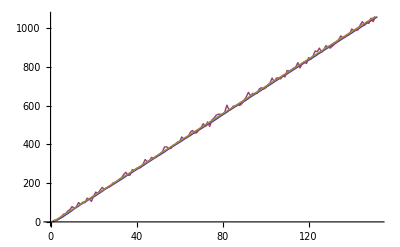

```mathematica
ListLinePlot[{KalmanSamplesX,NoisySamplesX,TrueSamplesX}]
```

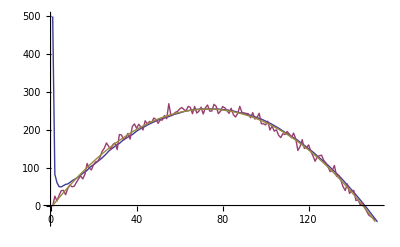

```mathematica
ListLinePlot[{KalmanSamplesY,NoisySamplesY,TrueSamplesY}]
```